```mathematica
Get[FileNameJoin[{NotebookDirectory[],"lyapunov.m"}]]
```

```mathematica
(F[x_,y_,z_]={16(y-x),x(45.92-z)-y,x y-4 z})//TableForm
```

16 (-x+y)
-y+x (45.92-z)
x y-4 z

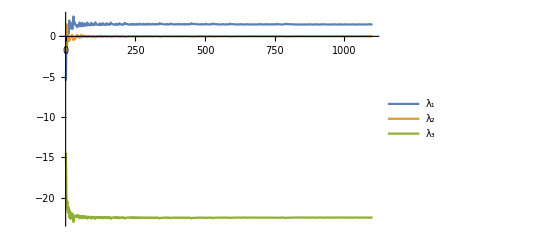

```mathematica
ListPlot[Transpose@(exps=CalculateLCE[F,{19,20,50},2000,0.1,1*^-4]),Joined->True,PlotLegends->{"λ_1","λ_2","λ_3"}]
```